# Mathematica Shortcuts and Modifying Lists

Math 213 - Math with Mathematica
Christopher Hanusa

## Aim

This tutorial first starts off with some best practices for Mathematica, and some shortcuts to make your life with Mathematica easier.  Then we develop tools for creating, accessing, and modifying lists.

Tip: You can evaluate ALL cells in this file in order using the Evaluation > Evaluate Notebook command.

## NOT losing your work

### Save your work

Mathematica is more likely to crash than other programs you’re used to, especially when you’re in the middle of a complex computation, or when it is right before your project is due.  Save your notebooks frequently.

### AutoSave!

It is possible to turn on the AutoSave feature of Mathematica.  What it will do is save your work every time you do an evaluation. (Shift-Return)  Follow these steps to turn it on:

Go to Preferences > Advanced

Click on “Open Option Inspector”

Ensure that “Global Preferences” is selected in the “Scope” pulldown menu.

In the Search Bar type in AutoSave

Click the checkbox next to “NotebookAutoSave”.

The only problem I have found with enabling AutoSave is that it slows down your coding process because it makes the computer work more often.  The piece of mind you get from knowing that your work is being saved regularly is worth it.  If things really start to go very slowly, it’s probably because your notebook is very very large.  When this happens to me, I save my work, I open a new notebook and bring over the most essential pieces of code into the new notebook and work from there.

### Undo

Mathematica has an undo command (Ctrl-Z or Option-Z is the keyboard shortcut). BUT it doesn’t always work, and don’t depend on it being able to undo more than one thing.

### Incremental Development

One way to avoid using an Undo command and that is a good programming practice that you should start to use is incremental development.  It boils down to three principles:

Always start with a piece of working code.

Make only one small modification at a time.

Test the new code to see if the change worked.

This is helpful because if you change something small and it breaks, it’s easy to find.  On the other hand, if you try to write a piece of code that is complex all in one go, then if it doesn’t work it will be much harder to find your error.

In a Mathematica notebook, the best way to do this is to start with a “Minimal Working Example”, such as a piece of code from the Documentation Center.  Then as you build your code and it becomes more and more complex:

Copy a piece of code that is working the way you want it to into a new cell just underneath.

Modify the code in the new cell in a new way.

Run the code in the new cell to see if it does what you want it to.  If so, repeat the cycle.  If not, check to see where it went wrong.

### Cloud Storage

It is good practice to save your work in multiple places so that you won’t lose your work if your computer dies.  One good way to do this is to use cloud storage.  Three good versions are Dropbox, Google Drive (available as part of the QC Google Apps for Education), and Microsoft OneDrive (available as part of your QMail account).  You should create an account on one of these services and make sure to upload your files to them.  In this way you will have access to them anywhere there is internet. If you have questions about this see me.

## Defining variables using the = operator

It is often helpful to define the output of a command to be able to reuse it later.  To do this, use the = operator:

```mathematica
a=Range[3]
```

{1,2,3}

```mathematica
a
```

{1,2,3}

If you don’t want to see the output of a command, you can end the line with a semicolon.

```mathematica
a=Range[4];
```

```mathematica
a
```

{1,2,3,4}

Important: it matters the order in which you evaluate commands.  For example, if you re-evaluate the first instance of a, it will return its last-defined definition, which is {1,2,3,4}.

I HIGHLY suggest that you give descriptive names to your variables. Since all built-in Mathematica commands start with a capital letter, a nice convention to use for your own variable names is to start with a lowercase letter and if variable is multiple words long, capitalize the start of each new word.

```mathematica
iAmANewVariable=Range[Pi,2Pi,Pi/2]
```

```mathematica
heyYouWhatsThatSound=Play[Sin[440 2Pi t],{t,0,1}]
```

(OK, the provided example names aren’t very descriptive, but you get the idea....it’s #likeAHashtag.)

## Shortcut: the % operator

A useful but slightly dangerous operator is %, which stands for the most recent output.  So, for instance, if you decide to make a list, and then decide you want to create a scatterplot, you can do the following:

```mathematica
Table[RandomInteger[{1,3}],{100}]
```

{2,2,2,1,3,2,3,2,2,3,3,1,1,1,1,3,1,2,1,3,3,1,2,1,2,3,3,1,2,1,1,3,3,1,2,2,1,1,2,3,1,2,1,1,2,1,1,3,3,1,3,2,3,3,3,3,1,2,3,3,2,2,1,2,3,3,1,2,3,1,3,2,3,3,2,1,3,3,2,2,3,2,3,2,2,1,3,1,2,2,3,1,2,1,2,1,3,3,2,1}

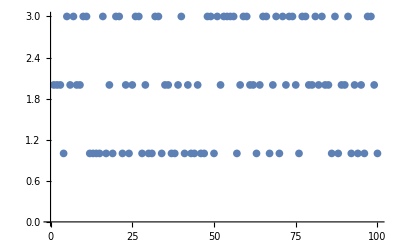

```mathematica
ListPlot[%]
```

The reason it is dangerous is related to the above discussion where the order in which you evaluate commands matters.  If you tried to re-evaluate the previous line of code, you would get an error, because you can’t create a scatterplot of a scatterplot!

```mathematica
ListPlot[%]
```

ListPlot::lpn: is not a list of numbers or pairs of numbers.

ListPlot[-Graphics-]

In the same vein is %% (for two outputs back); slightly more safe might be Out[n] to be explicit about wanting the nth output.  (But this will depend on the session in which you are working, so it would be different each time you re-open your notebook!!!!)  It is best to define a new variable when you think you will be using the output later.

## When you’ve gotten yourself in trouble

### When you don’t understand a command.

By now you should know that you can search in the Documentation Center when you want more information about a command.  You can also get quick information about a command directly in a Mathematica notebook by using the ? operator.

```mathematica
?Tally
```

Tally[list] tallies the elements in list, listing all distinct elements together with their multiplicities.
Tally[list,test] uses test to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

Notice the >> symbol at the end of the command information.  Click there to go directly to the Documentation Center.

You can also hover over a command to open up this quick command information or to go directly to the Documentation Center.

### When you define something you shouldn’t have.

Suppose you define a variable at some point:

```mathematica
x=10
```

10

Perhaps later in your file you wanted to generate the list {x+1,x+2,x+3} using the Table command:

```mathematica
Table[x+i,{i,3}]
```

{11,12,13}

Since x had been defined before, the generated list has no x’s in it.  When you run into such a problem, you use the Remove command:

```mathematica
Remove[x];
Table[x+i,{i,3}]
```

{1+x,2+x,3+x}

### When your code won’t stop running

We all get into infinite loops sometimes.  To stop Mathematica in the middle of a calculation, use (Option-.) or (Alt-.)  (That’s the period!)  
Try it here after removing the (* and *) which I used to comment out the command.

```mathematica
(* For[i=0,i≥0,i++,i] *)
```

## Comprehension Questions:

### 1. Practice using the % operator. First, define some list of even numbers by way of a Range or Table command. Then use % to divide the list by 2 to divide each entry by 2. Then use % to add 10 to each entry of the list. Last use % to give a scatterplot of this final list.

### 2. Use the ? operator to learn about the commands First and Rest.

## The Table command, Part Deux

### More Variables

The Table command can also create a list with two or more variables changing at a time.  Simply put two variable ranges as inputs.  In the following example, we consider all values of x from 1 to 3 and all values of y from 1 to 3 and multiply them together (because that's what the function x*y says to do).

```mathematica
array=Table[x*y,{x,3},{y,3}]
```

{{1,2,3},{2,4,6},{3,6,9}}

I would read this line of code as “Create a table of values of x times y, where x ranges from 1 to 3 and y ranges from 1 to 3, and define the result to be called ‘array’.”

### More Complicated Functions

The Table command is much more powerful than simply creating lists of numbers.  For instance, you can create lists of anything in the language of Mathematica:

Graphics objects:

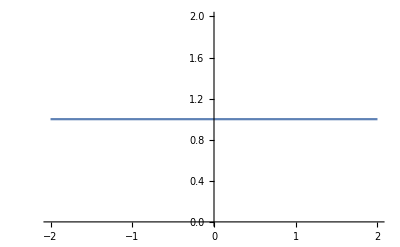
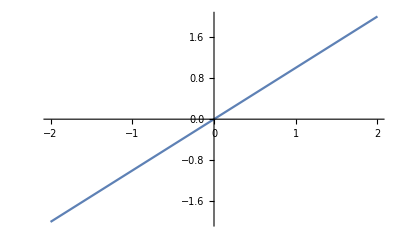

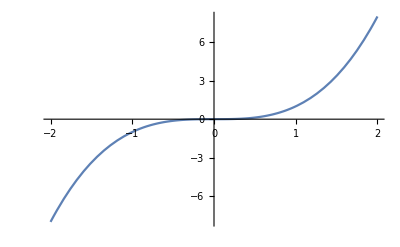
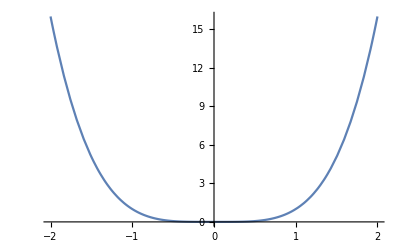
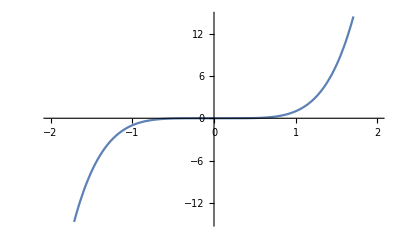
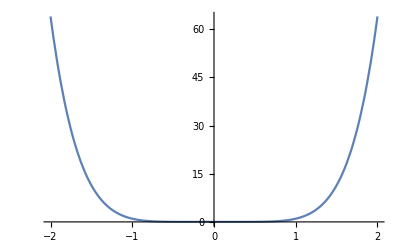
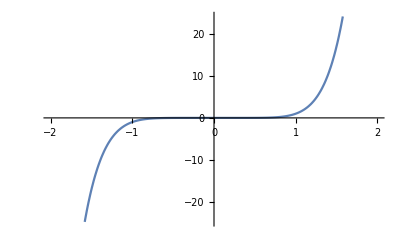
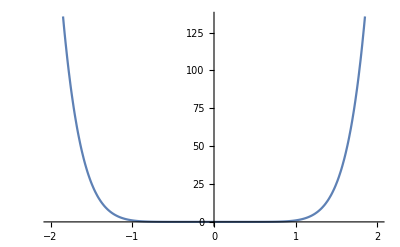

```mathematica
Table[Plot[x^n,{x,-2,2}],{n,0,10}]
```

Coordinates of the vertices of a hexagon:

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2}}

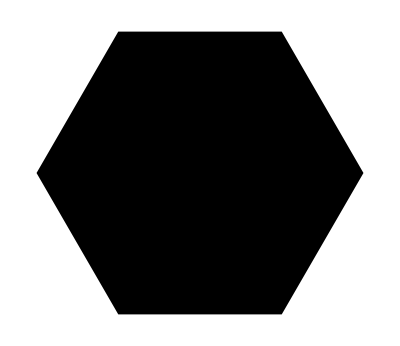

```mathematica
Table[{Cos[2π k/6],Sin[2π k/6]},{k,0,5}]
Graphics[Polygon[%]]
```

Pictures of polygons:

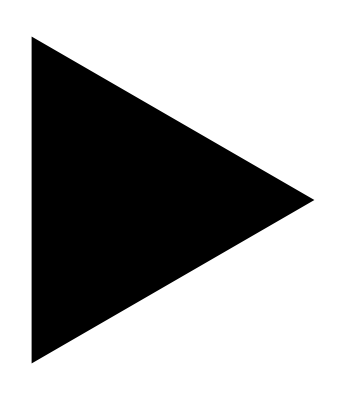
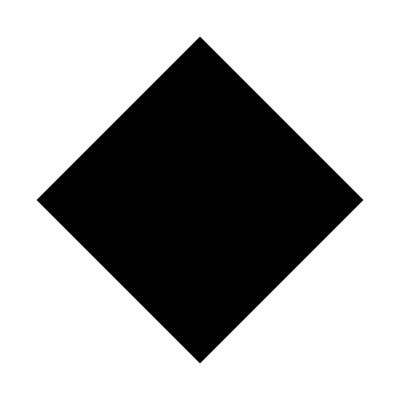
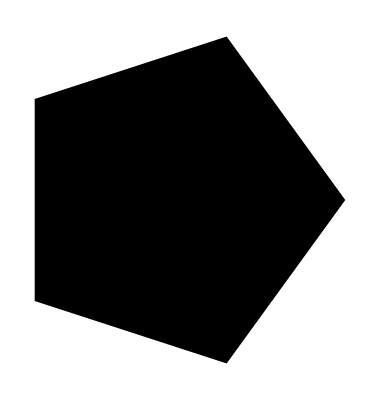
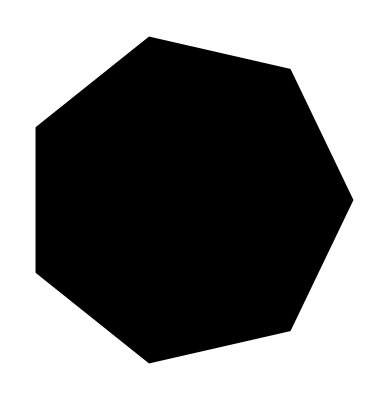
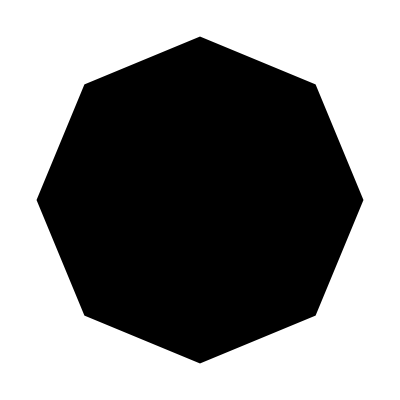
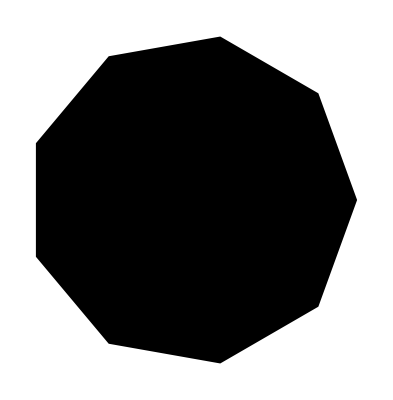
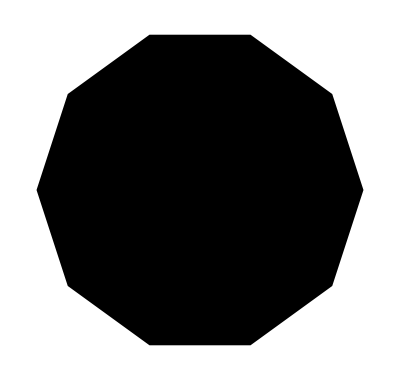
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Polygon[Table[{Cos[2π k/i],Sin[2π k/i]},{k,0,i-1}]]],{i,3,10}]
```

Colors:

```mathematica
Table[ColorData["Rainbow"][x],{x,0,1,.1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The Periodic Table of the Elements:

```mathematica
Table[ElementData[i,"Abbreviation"],{i,1,100}]
```

{H,He,Li,Be,B,C,N,O,F,Ne,Na,Mg,Al,Si,P,S,Cl,Ar,K,Ca,Sc,Ti,V,Cr,Mn,Fe,Co,Ni,Cu,Zn,Ga,Ge,As,Se,Br,Kr,Rb,Sr,Y,Zr,Nb,Mo,Tc,Ru,Rh,Pd,Ag,Cd,In,Sn,Sb,Te,I,Xe,Cs,Ba,La,Ce,Pr,Nd,Pm,Sm,Eu,Gd,Tb,Dy,Ho,Er,Tm,Yb,Lu,Hf,Ta,W,Re,Os,Ir,Pt,Au,Hg,Tl,Pb,Bi,Po,At,Rn,Fr,Ra,Ac,Th,Pa,U,Np,Pu,Am,Cm,Bk,Cf,Es,Fm}

## Comprehension Questions:

### 3. For each of the following Table commands, complete the following sub-questions. (a) BEFORE EVALUATING THE COMMAND, what list do you expect the command to give? Or do you expect an error? (b) Now, evaluate the command. Did it do what you expect it to do? (c) If not, figure out what went wrong with your reasoning.

```mathematica
Table[{s,7,9},{t,3,5}]
```

```mathematica
Table[{x,y},{x,2,4},{y,5,7}]
```

```mathematica
Table[xy,{x,2,4},{y,5,7}]
```

```mathematica
Table[Plot[x^n,{n,-2,2}],{x,1,10}]
```

```mathematica
Table[CountryData[country,"Population"],{country,{"France","United States","China"}}]
```

{64101308 people,322422965 people,1364773138 people}

### 4. Determine which Table commands give the following lists. There are multiple solutions for each one.

```mathematica
{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}
```

```mathematica
{{{0,0},{0,1},{0,2}},
{{1,0},{1,1},{1,2}},
{{2,0},{2,1},{2,2}}}
```

```mathematica
{{5,5,5},{6,6,6},{7,7,7},{8,8,8},{9,9,9},{10,10,10}}
```

```mathematica
{{"France","has",Quantity[64101308, "People"]},{"United States","has",Quantity[322422965, "People"]},{"China","has",Quantity[1364773138, "People"]}}
```

#### Solutions

```mathematica
Table[Range[i],{i,5}]
```

```mathematica
Table[{i,j},{i,0,2},{j,0,2}]
```

```mathematica
Table[{i,i,i},{i,5,10}]
```

```mathematica
Table[{country,"has",CountryData[country,"Population"]},{country,{"France","United States","China"}}]
```

## Challenge Questions

### 5. Determine which Table commands give the following lists.

```mathematica
{{B,B^2,B^3},{A B,A B^2,A B^3},{A^2 B,A^2 B^2,A^2 B^3},{A^3 B,A^3 B^2,A^3 B^3},{A^4 B,A^4 B^2,A^4 B^3}}
```

```mathematica
{{1},{2,2},{3,3,3},{4,4,4,4},{5,5,5,5,5}}
```

```mathematica
{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016]}
```

## Useful list commands

### Flatten

When there are nested lists and you would like to remove some of the extra braces, you should use Flatten.

```mathematica
list=Table[x*y,{x,3},{y,3}]
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
Flatten[list]
```

{1,2,3,2,4,6,3,6,9}

You can also specify how many layers of braces you want to remove.  For example, if your goal is to create a set of coordinate pairs (for points on a picture, for instance), then you wouldn’t want to remove all of the braces.

```mathematica
list2=Table[{x,y},{x,3},{y,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}}

```mathematica
Flatten[list2]
```

{1,1,1,2,1,3,2,1,2,2,2,3,3,1,3,2,3,3}

Instead, use the optional second argument to only remove one set of braces.

```mathematica
Flatten[list2,1]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

### Prepend and Append

When you want to add elements to the end of a preexisting list, use Append.  To add elements to the beginning, use Prepend.
This is often used in conjunction with redefining the preexisting list.

```mathematica
powersOfTen=Table[10^i,{i,0,5}]
```

{1,10,100,1000,10000,100000}

```mathematica
Append[powersOfTen,10^6]
```

{1,10,100,1000,10000,100000,1000000}

```mathematica
powersOfTen
```

{1,10,100,1000,10000,100000}

```mathematica
Prepend[powersOfTen,0]
```

{0,1,10,100,1000,10000,100000}

You can see that powersOfTen does not change when using Append or Prepend. 
You need to redefine powersOfTen if you want to actually add an entry to the list for future use.

```mathematica
powersOfTen=Append[powersOfTen,10^6]
```

{1,10,100,1000,10000,100000,1000000}

```mathematica
powersOfTen
```

{1,10,100,1000,10000,100000,1000000}

## Comprehension Questions:

### 5. For each of the following commands, complete the following sub-questions. (a) What list do you expect the command to give? Or do you expect an error? (b) Now evaluate the command. Did it do what you expect it to do? (c) If not, figure out what went wrong with your reasoning.

```mathematica
Flatten[{{{{1},2},3},4}]
```

```mathematica
Flatten[{{{{1},2},3},4},2]
```

```mathematica
Append[{1,2,3,4},{1}]
```

```mathematica
Append[{{1,2},{3,4}},5,6]
```

```mathematica
Append[{{1,2},{3,4}},{5,6}]
```

Discuss these answers with your neighbors.

### 6. Consider rolling two dice and taking the sum of the values. What is the average value for this sum? What is the average value for the product of two rolled dice? Three rolled dice? Four?

## Accessing parts of lists

### One entry of a list

It is often useful to access one or more of the entries of a list.  For this we use double square brackets [[n]], which is the shorthand notation for the command Part.

```mathematica
powersOfTen[[5]]
```

10000

```mathematica
Part[powersOfTen,5]
```

10000

### One entry of an array

When the list is a nested list, you can reference an entry of the list to choose a sublist, or any entry of any sublist.

```mathematica
nestedList={{1,2},{3,4},{5,6}};
```

```mathematica
nestedList[[2]]
```

{3,4}

```mathematica
nestedList[[2,1]]
```

3

### Multiple entries of a list

To extract multiple entries from a list, you can put a list of indices in the double square brackets.

```mathematica
powersOfTen[[{3,5}]]
```

{100,10000}

```mathematica
powersOfTen[[Range[3,5]]]
```

{100,1000,10000}

### Multiple entries of an array

To choose certain rows and columns of an array you can also use sets.  If you want all of the rows and only some of the columns (or vice versa), use the variable “All”.

```mathematica
products=Table[x*y^2,{x,1,10},{y,1,10}];
TableForm[products]
```

1 | 4 | 9 | 16 | 25 | 36 | 49 | 64 | 81 | 100
2 | 8 | 18 | 32 | 50 | 72 | 98 | 128 | 162 | 200
3 | 12 | 27 | 48 | 75 | 108 | 147 | 192 | 243 | 300
4 | 16 | 36 | 64 | 100 | 144 | 196 | 256 | 324 | 400
5 | 20 | 45 | 80 | 125 | 180 | 245 | 320 | 405 | 500
6 | 24 | 54 | 96 | 150 | 216 | 294 | 384 | 486 | 600
7 | 28 | 63 | 112 | 175 | 252 | 343 | 448 | 567 | 700
8 | 32 | 72 | 128 | 200 | 288 | 392 | 512 | 648 | 800
9 | 36 | 81 | 144 | 225 | 324 | 441 | 576 | 729 | 900
10 | 40 | 90 | 160 | 250 | 360 | 490 | 640 | 810 | 1000

Here we choose rows three, four and five, and columns 2, 4, and 8:

```mathematica
products[[Range[3,5],{2,4,8}]]
```

{{12,48,192},{16,64,256},{20,80,320}}

Here we choose the second entries of every row:

```mathematica
products[[All,2]]
```

{4,8,12,16,20,24,28,32,36,40}

## Comprehension Questions:

### 7. Write the code that takes entries 5 through 15 of this list primes

```mathematica
primes=Table[Prime[n],{n,1,20}]
```

### 8. What code should you use to choose the odd entries of the variable powersOfTen? Can you make it a general piece of code that works no matter how long the variable powersOfTen is?

### 9. Write the code that chooses the third entries of every column of products.

### 10. Here are two lists which represent the x- and y-coordinates of points, and an incorrect Table command that hopes to collect the points into a list of ordered x,y pairs. Figure out what is wrong with the command and fix it.

```mathematica
x={1,2,3,4,5}
y={2,5,10,17,26}
points=Table[{x[i],y[i]},{i,1,Length[x]}]
```

#### Solution:

You need to use double brackets to reference parts of a list.

```mathematica
points=Table[{x[[i]],y[[i]]},{i,1,Length[x]}]
```

## Exploration Question

### 11. Visit the Documentation Center entry for Getting Pieces Of Lists to see other commands Mathematica uses to take pieces of lists. What does the ;; operator do?